# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - ALL Decay width - Chi^2 )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

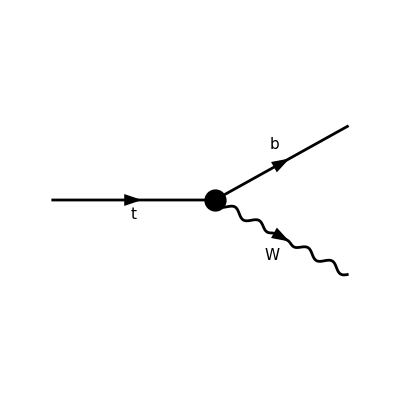

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

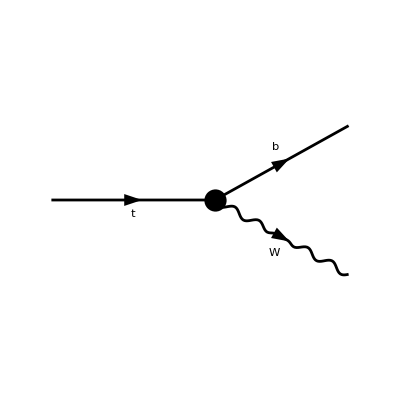

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

```mathematica
(* CALCULATION OF DECAY WIDTH and HELICITY FRACTION*)
```

```mathematica
Quit[]
```

```mathematica
g[c1_,c2_]:=a c1+b c2
```

```mathematica
X[c1_,c2_]:= g[c1,c2]-12
```

```mathematica
c1=0;
```

```mathematica
X[1,2]
```

-12+a+2 b

```mathematica
(*Compute decay width LEFT systematically*)
```

```mathematica
DecayWidthLeft[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 mt^2+32 √2 CtW g Lambda^6 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+16 √2 g Lambda^4 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq])+g^2 mt^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D]))+16 √2 g Lambda^2 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))//FullSimplify
```

```mathematica
(*Compute decay width LONGITUDINAL systematically*)
```

```mathematica
DecayWidth0[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(1024 Lambda^8 mt^3 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D])))//FullSimplify
```

```mathematica
(*Compute decay width TOTAL systematically*)
```

```mathematica
DecayWidthTotal[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))//FullSimplify
```

```mathematica
FL[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=DecayWidthLeft[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]/DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]//FullSimplify
```

```mathematica
F0[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=DecayWidth0[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]/DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]//FullSimplify
```

```mathematica
FLSM=FL[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]//FullSimplify
```

$Aborted

```mathematica
FLSM=FL/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

FL

```mathematica
F0SM=F0/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

F0

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

DecayWidthTotal

```mathematica
FR[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1-FL-F0//FullSimplify
```

```mathematica
(*Define parameters and constants based on PHYSICAL REVIEW D 100,056023 (2019)*)
Lambda=1000;e=0.31345;vev=246;g=0.6483;mb=4.78;mt=173.0; mw=80.379;CKM3x3=1;
FCGV["EL"]=e;Nc=1;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;
F0exp=0.687;
DecayWidthTotalexp=1.41;
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=0;
CtW=0;
CbW;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
rho={{1.0,0.0,0.0},{0.0,1.0,-0.87},{0.0,-0.87,1.0}};
sigma={0.19,0.018,0.013};
```

```mathematica
Sigma = Table[sigma[[i]] * rho[[i, j]] * sigma[[j]], {i, 3}, {j, 3}];
SigmaInv = Inverse[Sigma]
```

{{27.7008,0.,0.},{0.,12696.1,15293.9},{0.,15293.9,24340.4}}

```mathematica
Fth[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:={DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],F0[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],FL[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]};  

Fexp={DecayWidthTotalexp,F0exp,FLexp};     

Chi2[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=Module[{delta},delta=Fth[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]-Fexp; delta.SigmaInv.delta]
```

```mathematica
(* check for working*)
```

```mathematica
(*Fth[CtW,0,0,0,C1quWH3,0,0,0,0]*)
```

```mathematica
(*Module[{delta},delta=Fth[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]-Fexp; delta.SigmaInv.delta]*)
```

```mathematica
Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]
```

(0.0607269+0.0000154991 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000320433+0.00102447 Conjugate[CbW])+(-0.01059+0.0169288 Conjugate[CbW]) Conjugate[CbW]) (0.+27.7008 (0.0607269+0.0000154991 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000320433+0.00102447 Conjugate[CbW])+(-0.01059+0.0169288 Conjugate[CbW]) Conjugate[CbW]))+(-0.687+(1.02626+1.5142×10^-6 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000106811+0.000100086 Conjugate[CbW])+(-0.00353001+0.00165388 Conjugate[CbW]) Conjugate[CbW])/(1.47073+0.0000154991 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000320433+0.00102447 Conjugate[CbW])+(-0.01059+0.0169288 Conjugate[CbW]) Conjugate[CbW])) (0.+12696.1 (-0.687+(1.02626+1.5142×10^-6 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000106811+0.000100086 Conjugate[CbW])+(-0.00353001+0.00165388 Conjugate[CbW]) Conjugate[CbW])/(1.47073+0.0000154991 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000320433+0.00102447 Conjugate[CbW])+(-0.01059+0.0169288 Conjugate[CbW]) Conjugate[CbW]))+15293.9 (-0.319948+(28636.4+Conjugate[C1qdWH3] (-2.4499+1.04544×10^-15 Conjugate[CbW])-80.967 Conjugate[CbW])/(94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))))+(-0.319948+(28636.4+Conjugate[C1qdWH3] (-2.4499+1.04544×10^-15 Conjugate[CbW])-80.967 Conjugate[CbW])/(94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))) (0.+15293.9 (-0.687+(1.02626+1.5142×10^-6 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000106811+0.000100086 Conjugate[CbW])+(-0.00353001+0.00165388 Conjugate[CbW]) Conjugate[CbW])/(1.47073+0.0000154991 Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-0.000320433+0.00102447 Conjugate[CbW])+(-0.01059+0.0169288 Conjugate[CbW]) Conjugate[CbW]))+24340.4 (-0.319948+(28636.4+Conjugate[C1qdWH3] (-2.4499+1.04544×10^-15 Conjugate[CbW])-80.967 Conjugate[CbW])/(94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))))

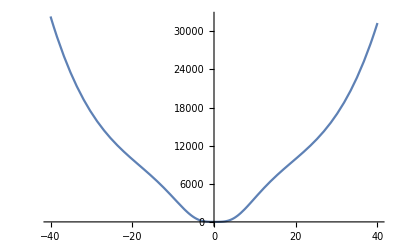

```mathematica
Plot[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,0,C2q2H4D,C3q2H4D,CudH4D],{CbW,-40,40}]
```

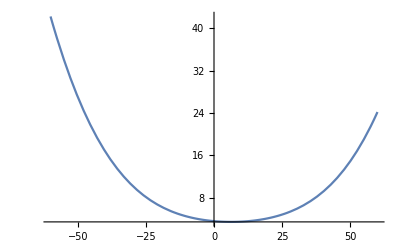

```mathematica
Plot[Chi2[CtW,0,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C1qdWH3,-60,60}]
```

```mathematica
d1=D[x^3+y^2+4x y,x]
```

3 x^2+4 y

```mathematica
d2=D[x^3+y^2+4x y,y]
```

4 x+2 y

```mathematica
NSolve[{d1==0,d2==0},{x,y}]
```

{{x→2.66667,y→-5.33333},{x→0.,y→0.}}

```mathematica
d11=D[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],C1qdWH3]//FullSimplify
```

((-3.32715×10^28+2.66176×10^-8 Conjugate[C1qdWH3]^15+Conjugate[C1qdWH3]^14 (-4.12724×10^-6+0.0000131953 Conjugate[CbW])+Conjugate[C1qdWH3]^13 (0.0155376+(-0.00190962+0.00305265 Conjugate[CbW]) Conjugate[CbW])+Conjugate[C1qdWH3]^12 (-2.06123+Conjugate[CbW] (6.67555+(-0.410224+0.437179 Conjugate[CbW]) Conjugate[CbW]))+Conjugate[C1qdWH3]^11 (3772.1+Conjugate[CbW] (-817.462+Conjugate[CbW] (1323.73+Conjugate[CbW] (-54.2301+43.3451 Conjugate[CbW]))))+Conjugate[C1qdWH3]^10 (-622146.+Conjugate[CbW] (1.37131×10^6+Conjugate[CbW] (-148590.+Conjugate[CbW] (160409.+Conjugate[CbW] (-4928.71+3151.54 Conjugate[CbW])))))+Conjugate[C1qdWH3]^9 (5.24682×10^9+Conjugate[CbW] (-2.05614×10^8+Conjugate[CbW] (2.26603×10^8+Conjugate[CbW] (-1.63692×10^7+Conjugate[CbW] (1.32535×10^7+Conjugate[CbW] (-325779.+173593. Conjugate[CbW]))))))+Conjugate[C1qdWH3]^8 (-4.86583×10^11+Conjugate[CbW] (1.56063×10^12+Conjugate[CbW] (-3.05791×10^10+Conjugate[CbW] (2.24671×10^10+Conjugate[CbW] (-1.21722×10^9+Conjugate[CbW] (7.88427×10^8+Conjugate[CbW] (-1.615×10^7+7.37625×10^6 Conjugate[CbW])))))))+Conjugate[C1qdWH3]^7 (1.40723×10^15+Conjugate[CbW] (-1.28649×10^14+Conjugate[CbW] (2.06309×10^14+Conjugate[CbW] (-2.69497×10^12+Conjugate[CbW] (1.48504×10^12+Conjugate[CbW] (-6.43651×10^10+Conjugate[CbW] (3.47424×10^10+Conjugate[CbW] (-6.09994×10^8+2.43778×10^8 Conjugate[CbW]))))))))+Conjugate[C1qdWH3]^6 (-9.01129×10^16+Conjugate[CbW] (3.25554×10^17+Conjugate[CbW] (-1.48811×10^16+Conjugate[CbW] (1.59095×10^16+Conjugate[CbW] (-1.55866×10^14+Conjugate[CbW] (6.87107×10^13+Conjugate[CbW] (-2.48174×10^12+Conjugate[CbW] (1.14821×10^12+Conjugate[CbW] (-1.76398×10^10+6.26629×10^9 Conjugate[CbW])))))))))+Conjugate[C1qdWH3]^5 (1.3321×10^20+Conjugate[CbW] (-1.78689×10^19+Conjugate[CbW] (3.22779×10^19+Conjugate[CbW] (-9.83613×10^17+Conjugate[CbW] (7.8869×10^17+Conjugate[CbW] (-6.18147×10^15+Conjugate[CbW] (2.27083×10^15+Conjugate[CbW] (-7.03024×10^13+Conjugate[CbW] (2.84604×10^13+Conjugate[CbW] (-3.88653×10^11+1.24257×10^11 Conjugate[CbW]))))))))))+Conjugate[C1qdWH3]^4 (-5.42625×10^21+Conjugate[CbW] (2.20124×10^22+Conjugate[CbW] (-1.47638×10^21+Conjugate[CbW] (1.77792×10^21+Conjugate[CbW] (-4.06344×10^19+Conjugate[CbW] (2.60655×10^19+Conjugate[CbW] (-1.70244×10^17+Conjugate[CbW] (5.36063×10^16+Conjugate[CbW] (-1.45214×10^15+Conjugate[CbW] (5.2255×10^14+Conjugate[CbW] (-6.42231×10^12+1.86663×10^12 Conjugate[CbW])))))))))))+Conjugate[C1qdWH3]^3 (4.30557×10^24+Conjugate[CbW] (-7.17332×10^23+Conjugate[CbW] (1.45498×10^24+Conjugate[CbW] (-6.50573×10^22+Conjugate[CbW] (5.87588×10^22+Conjugate[CbW] (-1.07434×10^21+Conjugate[CbW] (5.74294×10^20+Conjugate[CbW] (-3.21508×10^18+Conjugate[CbW] (8.85821×10^17+Conjugate[CbW] (-2.13298×10^16+Conjugate[CbW] (6.90793×10^15+Conjugate[CbW] (-7.71825×10^13+2.05635×10^13 Conjugate[CbW]))))))))))))+Conjugate[C1qdWH3]^2 (-8.23745×10^25+Conjugate[CbW] (4.26886×10^26+Conjugate[CbW] (-3.55608×10^25+Conjugate[CbW] (4.80859×10^25+Conjugate[CbW] (-1.61257×10^24+Conjugate[CbW] (1.16516×10^24+Conjugate[CbW] (-1.77531×10^22+Conjugate[CbW] (8.13425×10^21+Conjugate[CbW] (-3.98459×10^19+Conjugate[CbW] (9.75853×10^18+Conjugate[CbW] (-2.11479×10^17+Conjugate[CbW] (6.22639×10^16+Conjugate[CbW] (-6.37703×10^14+1.56832×10^14 Conjugate[CbW])))))))))))))+Conjugate[C1qdWH3] (5.59907×10^27+Conjugate[CbW] (-5.44481×10^27+Conjugate[CbW] (1.41082×10^28+Conjugate[CbW] (-7.83501×10^26+Conjugate[CbW] (7.94598×10^26+Conjugate[CbW] (-2.13175×10^25+Conjugate[CbW] (1.28358×10^25+Conjugate[CbW] (-1.67635×10^23+Conjugate[CbW] (6.72074×10^22+Conjugate[CbW] (-2.92638×10^20+Conjugate[CbW] (6.45022×10^19+Conjugate[CbW] (-1.27076×10^18+Conjugate[CbW] (3.42961×10^17+Conjugate[CbW] (-3.24239×10^15+7.40452×10^14 Conjugate[CbW]))))))))))))))+Conjugate[CbW] (1.85044×10^29+Conjugate[CbW] (-8.99731×10^28+Conjugate[CbW] (1.55421×10^29+Conjugate[CbW] (-6.4735×10^27+Conjugate[CbW] (5.25215×10^27+Conjugate[CbW] (-1.17421×10^26+Conjugate[CbW] (6.06016×10^25+Conjugate[CbW] (-6.92524×10^23+Conjugate[CbW] (2.46794×10^23+Conjugate[CbW] (-9.67142×10^20+Conjugate[CbW] (1.93794×10^20+Conjugate[CbW] (-3.4998×10^18+Conjugate[CbW] (8.71889×10^17+Conjugate[CbW] (-7.65414×10^15+1.63142×10^15 Conjugate[CbW]))))))))))))))) Conjugate'[C1qdWH3])/((94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))^3 (94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))^3)

```mathematica
d22=D[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],CbW]//FullSimplify
```

((-1.09959×10^30+8.79687×10^-7 Conjugate[C1qdWH3]^15+Conjugate[C1qdWH3]^14 (-0.000136402+0.000436093 Conjugate[CbW])+Conjugate[C1qdWH3]^13 (0.513504+(-0.0631113+0.100887 Conjugate[CbW]) Conjugate[CbW])+Conjugate[C1qdWH3]^12 (-68.1218+Conjugate[CbW] (220.621+Conjugate[CbW] (-13.5575+14.4484 Conjugate[CbW])))+Conjugate[C1qdWH3]^11 (124665.+Conjugate[CbW] (-27016.4+Conjugate[CbW] (43748.+Conjugate[CbW] (-1792.26+1432.52 Conjugate[CbW]))))+Conjugate[C1qdWH3]^10 (-2.05614×10^7+Conjugate[CbW] (4.53206×10^7+Conjugate[CbW] (-4.91077×10^6+Conjugate[CbW] (5.30138×10^6+Conjugate[CbW] (-162889.+104156. Conjugate[CbW])))))+Conjugate[C1qdWH3]^9 (1.73403×10^11+Conjugate[CbW] (-6.79536×10^9+Conjugate[CbW] (7.48903×10^9+Conjugate[CbW] (-5.40989×10^8+Conjugate[CbW] (4.38015×10^8+Conjugate[CbW] (-1.07667×10^7+5.73708×10^6 Conjugate[CbW]))))))+Conjugate[C1qdWH3]^8 (-1.60811×10^13+Conjugate[CbW] (5.15773×10^13+Conjugate[CbW] (-1.01061×10^12+Conjugate[CbW] (7.42518×10^11+Conjugate[CbW] (-4.02282×10^10+Conjugate[CbW] (2.60568×10^10+Conjugate[CbW] (-5.33745×10^8+2.43778×10^8 Conjugate[CbW])))))))+Conjugate[C1qdWH3]^7 (4.65078×10^16+Conjugate[CbW] (-4.25174×10^15+Conjugate[CbW] (6.81834×10^15+Conjugate[CbW] (-8.90662×10^13+Conjugate[CbW] (4.90791×10^13+Conjugate[CbW] (-2.12721×10^12+Conjugate[CbW] (1.14821×10^12+Conjugate[CbW] (-2.01598×10^10+8.05666×10^9 Conjugate[CbW]))))))))+Conjugate[C1qdWH3]^6 (-2.97815×10^18+Conjugate[CbW] (1.07593×10^19+Conjugate[CbW] (-4.91806×10^17+Conjugate[CbW] (5.25793×10^17+Conjugate[CbW] (-5.15123×10^15+Conjugate[CbW] (2.27083×10^15+Conjugate[CbW] (-8.20194×10^13+Conjugate[CbW] (3.79472×10^13+Conjugate[CbW] (-5.82979×10^11+2.07095×10^11 Conjugate[CbW])))))))))+Conjugate[C1qdWH3]^5 (4.40249×10^21+Conjugate[CbW] (-5.90551×10^20+Conjugate[CbW] (1.06675×10^21+Conjugate[CbW] (-3.25075×10^19+Conjugate[CbW] (2.60655×10^19+Conjugate[CbW] (-2.04292×10^17+Conjugate[CbW] (7.50489×10^16+Conjugate[CbW] (-2.32343×10^15+Conjugate[CbW] (9.40591×10^14+Conjugate[CbW] (-1.28446×10^13+4.10659×10^12 Conjugate[CbW]))))))))))+Conjugate[C1qdWH3]^4 (-1.79333×10^23+Conjugate[CbW] (7.27491×10^23+Conjugate[CbW] (-4.8793×10^22+Conjugate[CbW] (5.87588×10^22+Conjugate[CbW] (-1.34293×10^21+Conjugate[CbW] (8.61441×10^20+Conjugate[CbW] (-5.6264×10^18+Conjugate[CbW] (1.77164×10^18+Conjugate[CbW] (-4.79921×10^16+Conjugate[CbW] (1.72698×10^16+Conjugate[CbW] (-2.12252×10^14+6.16905×10^13 Conjugate[CbW])))))))))))+Conjugate[C1qdWH3]^3 (1.42295×10^26+Conjugate[CbW] (-2.37072×10^25+Conjugate[CbW] (4.80859×10^25+Conjugate[CbW] (-2.15009×10^24+Conjugate[CbW] (1.94193×10^24+Conjugate[CbW] (-3.55061×10^22+Conjugate[CbW] (1.89799×10^22+Conjugate[CbW] (-1.06256×10^20+Conjugate[CbW] (2.92756×10^19+Conjugate[CbW] (-7.04931×10^17+Conjugate[CbW] (2.28301×10^17+Conjugate[CbW] (-2.55081×10^15+6.79606×10^14 Conjugate[CbW]))))))))))))+Conjugate[C1qdWH3]^2 (-2.72241×10^27+Conjugate[CbW] (1.41082×10^28+Conjugate[CbW] (-1.17525×10^27+Conjugate[CbW] (1.5892×10^27+Conjugate[CbW] (-5.32938×10^25+Conjugate[CbW] (3.85074×10^25+Conjugate[CbW] (-5.86723×10^23+Conjugate[CbW] (2.6883×10^23+Conjugate[CbW] (-1.31687×10^21+Conjugate[CbW] (3.22511×10^20+Conjugate[CbW] (-6.98921×10^18+Conjugate[CbW] (2.05777×10^18+Conjugate[CbW] (-2.10755×10^16+5.18316×10^15 Conjugate[CbW])))))))))))))+Conjugate[C1qdWH3] (1.85044×10^29+Conjugate[CbW] (-1.79946×10^29+Conjugate[CbW] (4.66264×10^29+Conjugate[CbW] (-2.5894×10^28+Conjugate[CbW] (2.62607×10^28+Conjugate[CbW] (-7.04526×10^26+Conjugate[CbW] (4.24211×10^26+Conjugate[CbW] (-5.5402×10^24+Conjugate[CbW] (2.22115×10^24+Conjugate[CbW] (-9.67142×10^21+Conjugate[CbW] (2.13174×10^21+Conjugate[CbW] (-4.19976×10^19+Conjugate[CbW] (1.13346×10^19+Conjugate[CbW] (-1.07158×10^17+2.44713×10^16 Conjugate[CbW]))))))))))))))+Conjugate[CbW] (6.11554×10^30+Conjugate[CbW] (-2.97353×10^30+Conjugate[CbW] (5.13653×10^30+Conjugate[CbW] (-2.13943×10^29+Conjugate[CbW] (1.73579×10^29+Conjugate[CbW] (-3.88066×10^27+Conjugate[CbW] (2.00283×10^27+Conjugate[CbW] (-2.28873×10^25+Conjugate[CbW] (8.15632×10^24+Conjugate[CbW] (-3.19632×10^22+Conjugate[CbW] (6.40473×10^21+Conjugate[CbW] (-1.15665×10^20+Conjugate[CbW] (2.88152×10^19+Conjugate[CbW] (-2.52963×10^17+5.39169×10^16 Conjugate[CbW]))))))))))))))) Conjugate'[CbW])/((94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))^3 (94890.8+1. Conjugate[C1qdWH3]^2+Conjugate[C1qdWH3] (-20.6743+66.0982 Conjugate[CbW])+Conjugate[CbW] (-683.266+1092.24 Conjugate[CbW]))^3)

```mathematica
Solu=NSolve[{d11==0,d22==0},{C1qdWH3,CbW}]
```

$Aborted

```mathematica
Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C1qdWH3,CbW}]
```

{3.47435,{C1qdWH3→0.77396,CbW→0.168386}}

```mathematica
bestFit=Last@Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C1qdWH3,CbW}]
```

{C1qdWH3→0.77396,CbW→0.168386}

```mathematica
chi2min=First@Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C1qdWH3,CbW}]
```

3.47435

```mathematica
shiftedChi2[c1_,ct_]:=Chi2[c1+bestFit[[1,2]],ct+bestFit[[2,2]]]
```

```mathematica
shiftedChi2[C1qdWH3,CbW]
```

Chi2[0.77396+C1qdWH3,0.168386+CbW]

```mathematica
chi2min=3.47435;
deltaChi2=2.3;  (*for 68% CL with 2 parameters*)
deltaChi22=5.99;  (*for 95% CL with 2 parameters*)
```

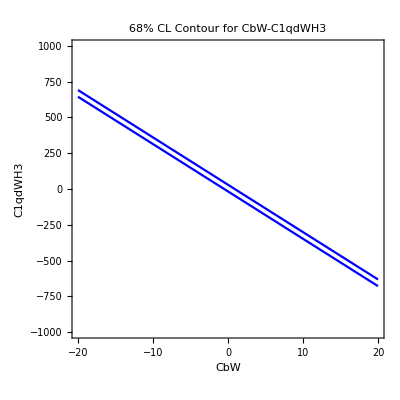

```mathematica
ContourPlot[Evaluate[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]==chi2min+deltaChi2],{CbW,-20,20},{C1qdWH3,-1000,1000},AspectRatio->1,PlotPoints->100,FrameLabel->{"CbW","C1qdWH3"},PlotLabel->"68% CL Contour for CbW-C1qdWH3",ContourStyle->Blue]
```

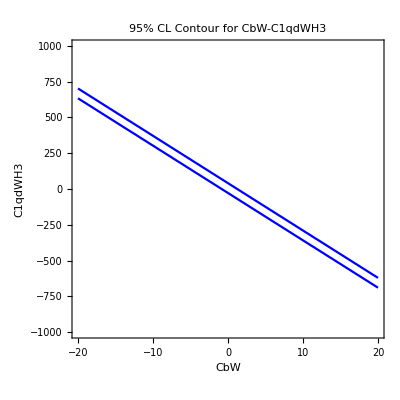

```mathematica
ContourPlot[Evaluate[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]==chi2min+deltaChi22],{CbW,-20,20},{C1qdWH3,-1000,1000},AspectRatio->1,PlotPoints->100,FrameLabel->{"CbW","C1qdWH3"},PlotLabel->"95% CL Contour for CbW-C1qdWH3",ContourStyle->Blue]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```